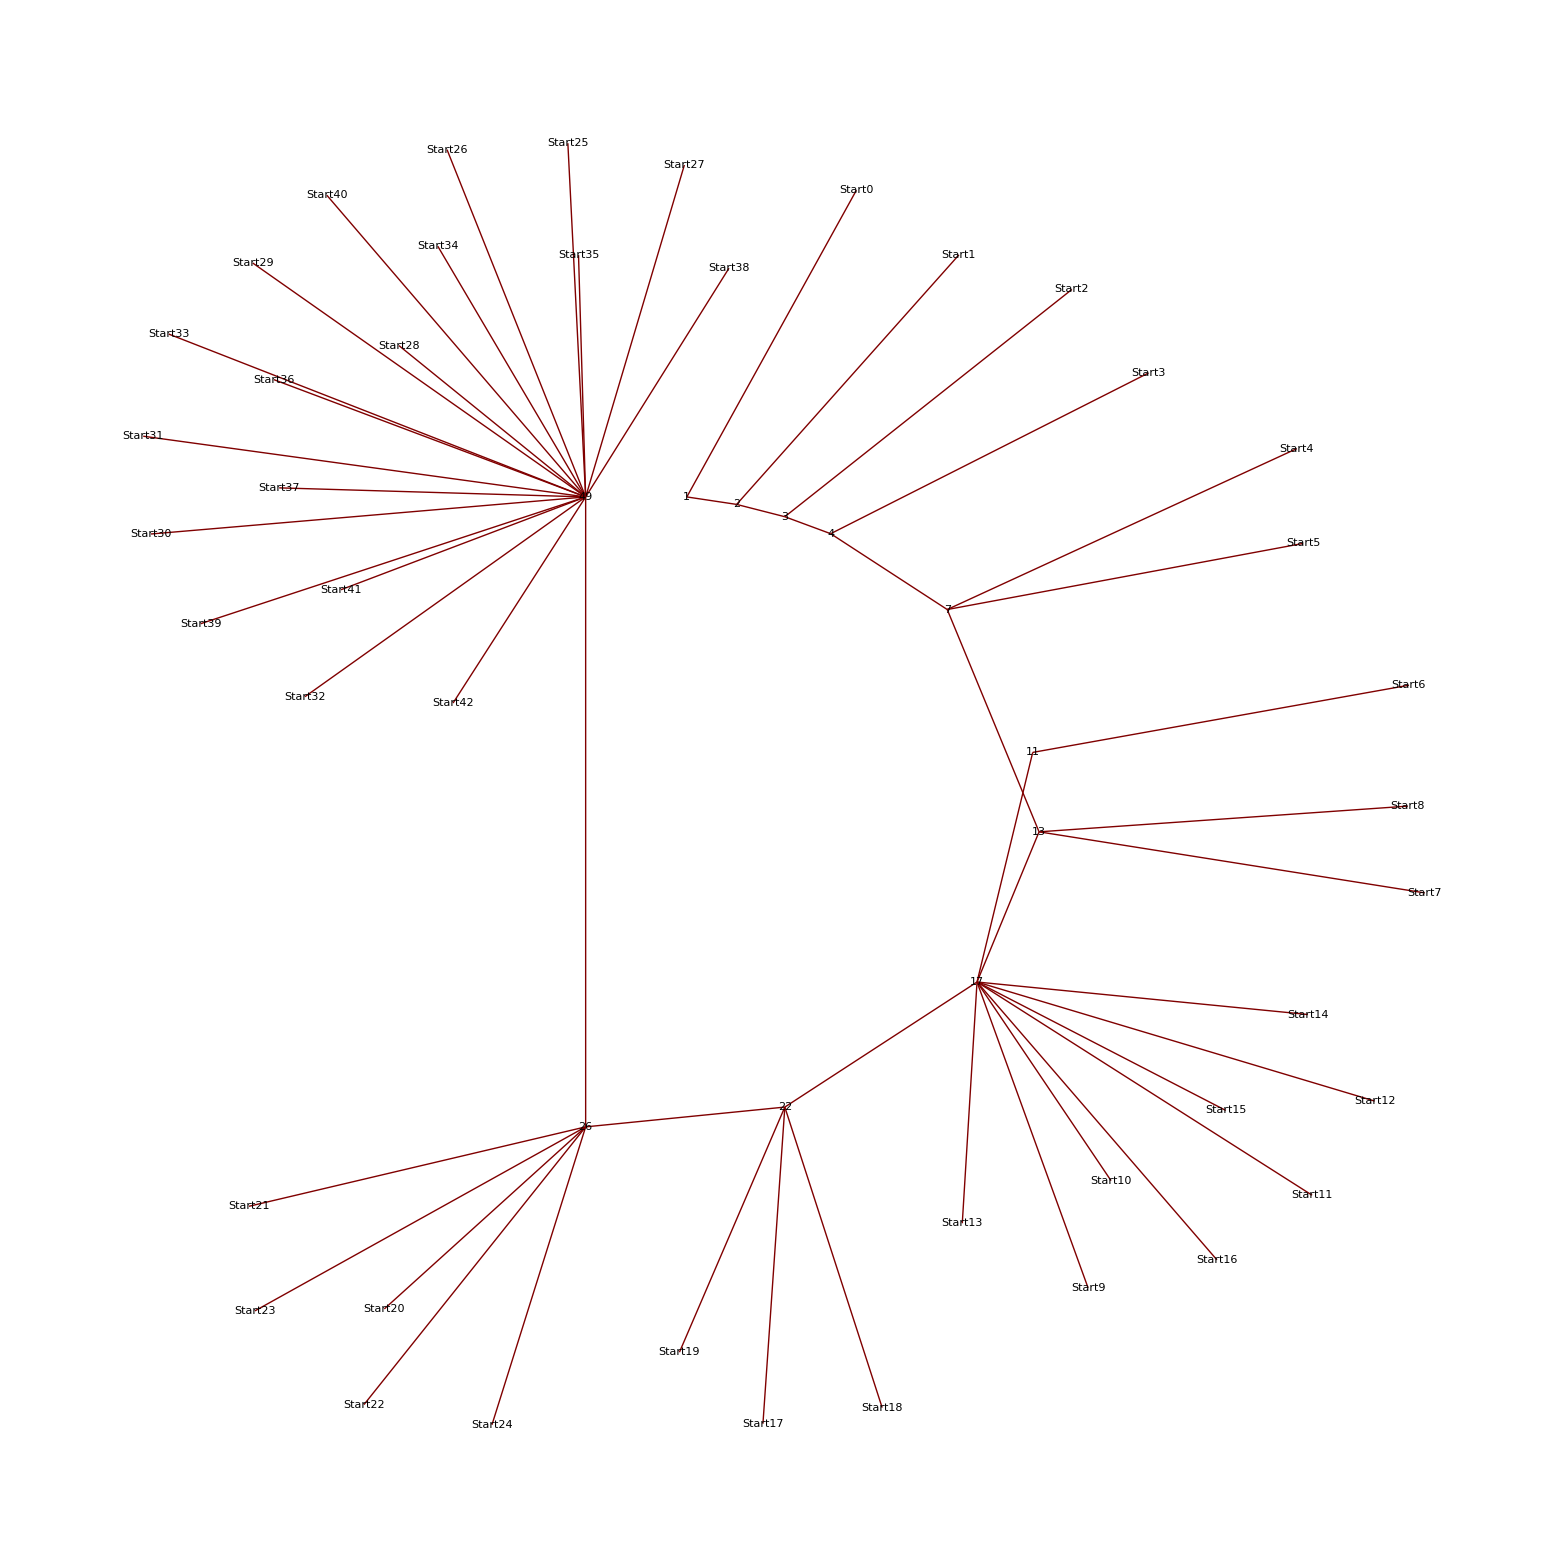

```mathematica
With[{range=50},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotes[VoteList[start,range,{7,11,13,17}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

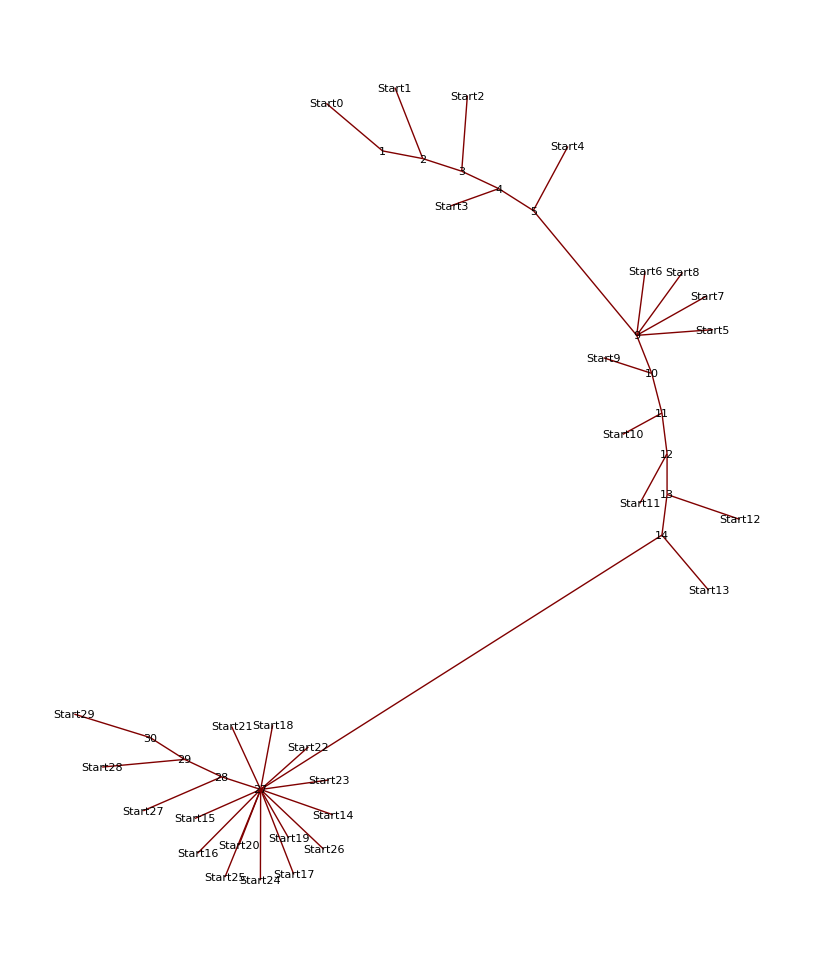

```mathematica
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotes[VoteList[start,range,{3}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

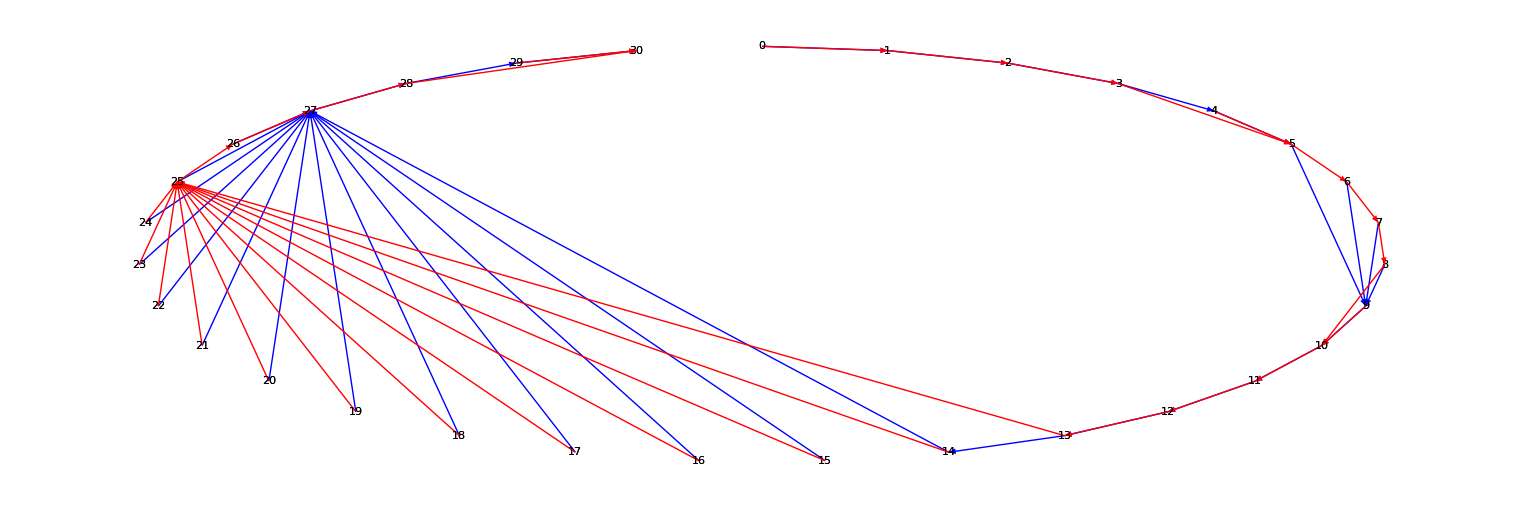

```mathematica
Show[
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{3}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{3*Sin[i*2*Pi / 31], Cos[i * 2 * Pi / 31]}, {i,0,range}],
ImageSize->Large,
EdgeRenderingFunction->({Blue, Arrowheads[.01],Arrow[#1]}&)
]
],
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{5}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{3*Sin[i*2*Pi / 31], Cos[i * 2 * Pi / 31]}, {i,0,range}],
ImageSize->Large,
EdgeRenderingFunction->({Red, Arrowheads[.01],Arrow[#1]}&)
]
]
]
```

```mathematica
With[{range=50},
GraphPlot[
{
Table[
GraphFromVotes[VoteList[start,range,{3}], start, Directive[{Red}]],
{start,0,range-1}]
,
Table[
GraphFromVotes[VoteList[start,range,{5}], start, Directive[{Blue}]],
{start,0,range-1}]
},
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

GraphPlot::grph: {{« 1 »}, {« 1 »}} is not a valid graph.

GraphPlot[«1»]

```mathematica
VoteGraph[0,50, {3,5}]
```

{0→0,0→0,1→1,1→1,2→3,2→2,3→3,3→5,5→9,5→5,9→9,9→10,10→10,10→10,11→12,11→11,12→12,12→12,13→13,13→25,25→27,25→25,27→27,27→27,28→28,28→30,30→30,30→30,31→31,31→31,32→36,32→32,36→36,36→36,37→37,37→37,38→39,38→50,50→81,50→50}

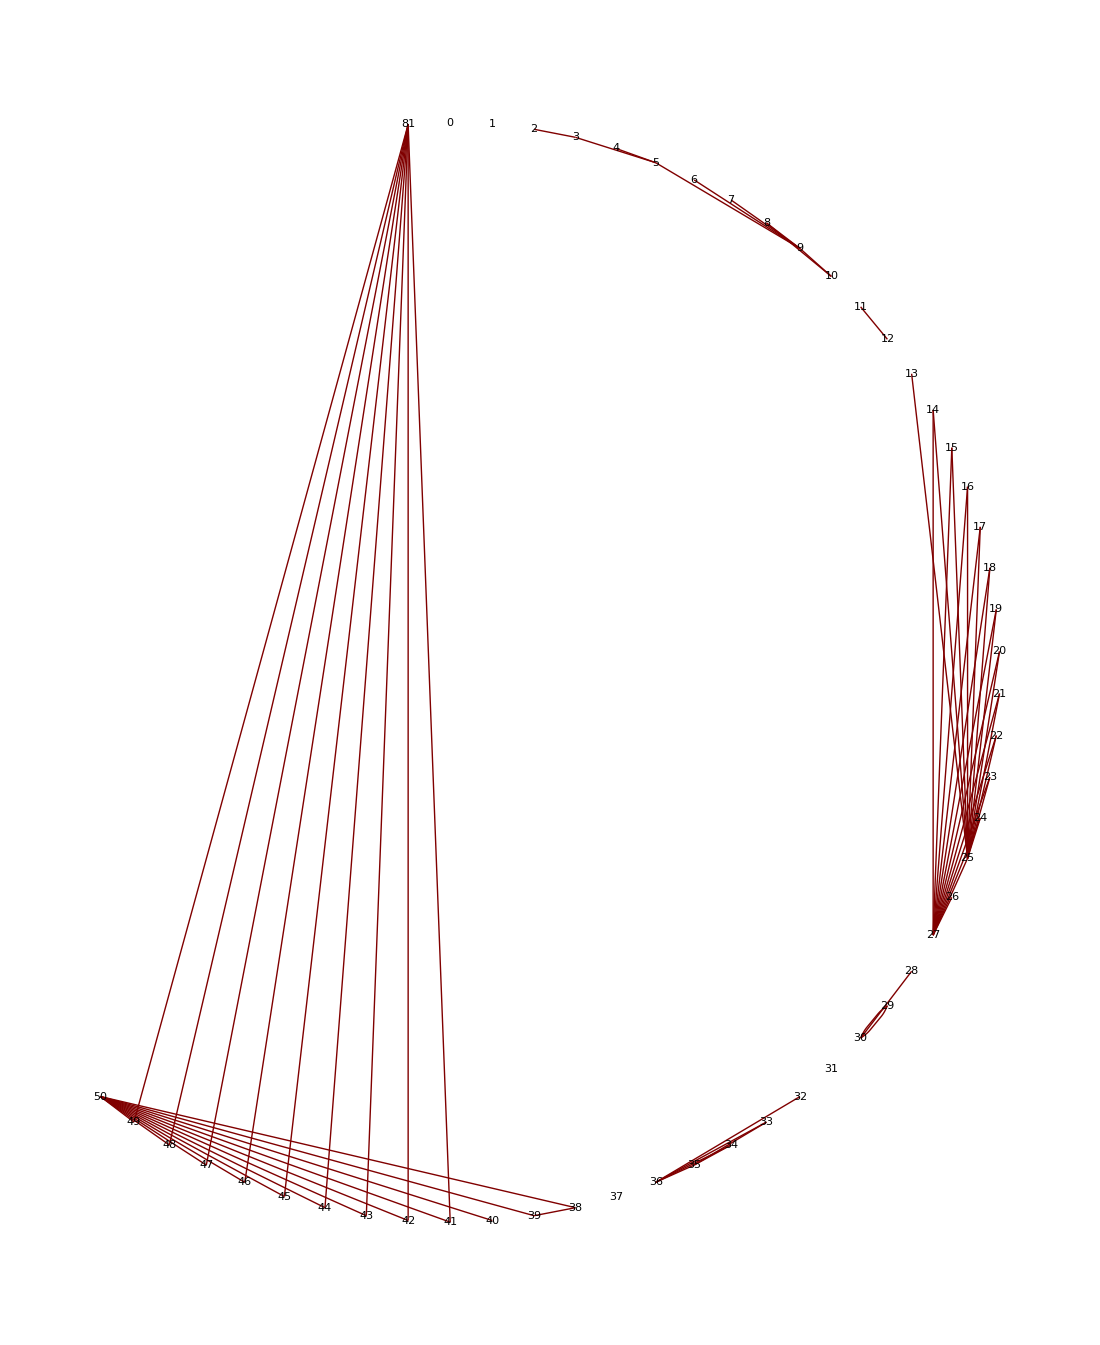

```mathematica
With[{range=50},
GraphPlot[
VoteGraph[0,49, {3,5}],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->Automatic,
DirectedEdges->False,
SelfLoopStyle->None,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 82], Cos[i * 2 * Pi / 82]}, {i,0,100}],
ImageSize->Large
]
]
```

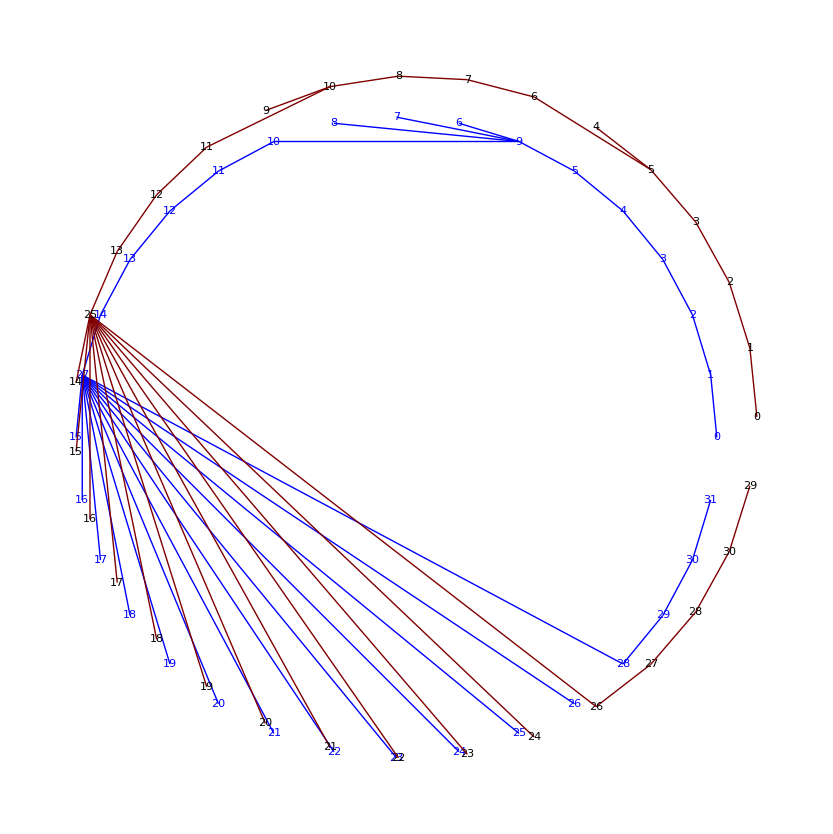

```mathematica
Show[
With[{range=31},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{3}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
ImageSize->Large,
Method->"CircularEmbedding",
PlotStyle->Blue
]
],
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{5}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
ImageSize->Large,
Method->"CircularEmbedding"
]
]
]
```

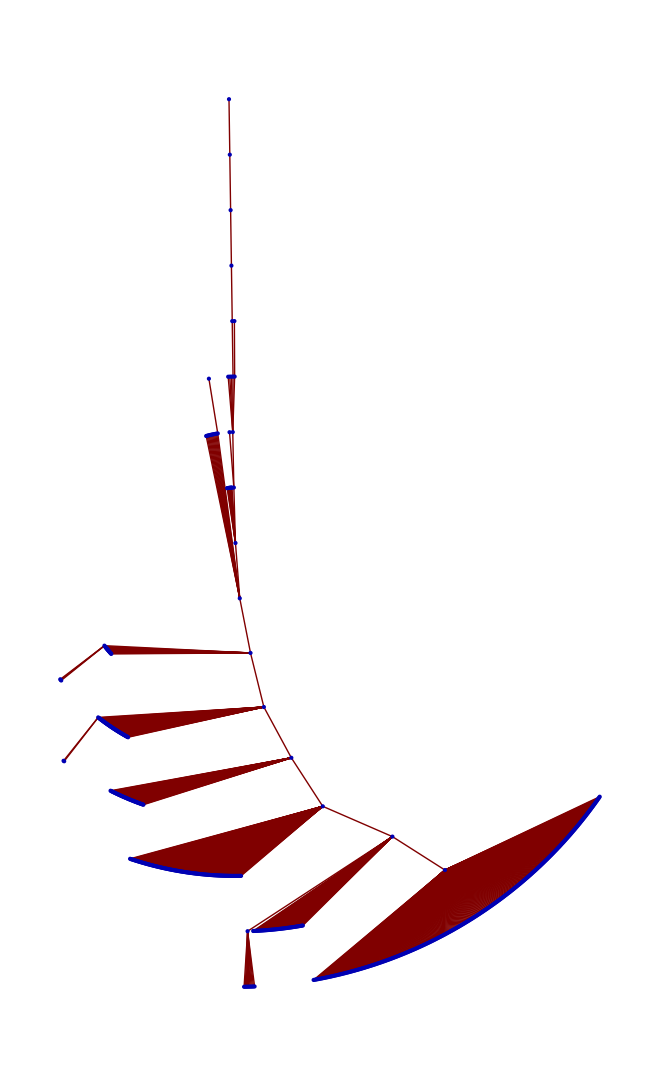

```mathematica
With[{range=1000},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{3,5,7,11}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->False,
MultiedgeStyle->None,
DirectedEdges->False,
ImageSize->Large
]
]
```

```mathematica
With[{range=10^5, tuple={7,11,13,17}},
With[{mainPath=Map[First,VoteList[0,range,tuple, {}]]},
GraphPlot[
CombineGraphs[
Append[
Table[
GraphFromVotesShort[VoteList[start,range,tuple,mainPath], start],
{start,1,range-1}],
Table[mainPath[[pos-1]]->mainPath[[pos]], {pos,2, Length[mainPath]}]
]
],
 EdgeLabeling->False,
VertexLabeling->False,
MultiedgeStyle->None,
DirectedEdges->False,
ImageSize->Large
]
]
]
```

-Graphics-

```mathematica
Map[First, VoteList[0,100,{7,11,13,17}]]
```

{0,1,2,3,4,7,13,17,22,26,49,52,55,56,57,58,59,65}

```mathematica
VoteList[5,10,{7,11,13,17},Map[First, VoteList[0,100,{7,11,13,17}]]]
```

{{5,{2,0,0,0}},{7,{0,4,6,0}}}

```mathematica
With[{range=IntegerPart[(10^6)], tuple={3,5,7,11}},
With[{mainPath=Map[First,VoteList[0,range,tuple, {}]]},
ListPlot[
Table[
If[Mod[start,1000]==0,PrintTemporary[ToString[N[start / range * 100]] ]];{start,Length[VoteList[start,range,tuple,mainPath]]},
{start,1,range-1}],
PlotRange->All
]
]
]
```

$Aborted

```mathematica
drie = With[{range=IntegerPart[(10^5)], tuple={3,5,7,11}},
With[{mainPath=Map[First,VoteList[0,range,tuple, {}]]},
Select[
Table[
{start,Length[VoteList[start,range,tuple,mainPath]]},
{start,1,range-1}],
#[[2]]> 2 &
]
]
]
```

{{4,3},{13,3},{38,3},{39,3},{40,3},{61,3},{62,3},{303,3},{304,3},{305,3},{306,3},{307,3},{308,3},{309,3},{310,3},{311,3},{312,3},{1094,3},{1095,3},{1096,3},{1097,3},{1098,3},{1099,3},{1100,3},{1101,3},{1102,3},{1103,3},{1104,3},{1105,3},{1106,3},{1107,3},{1108,3},{1109,3},{1110,3},{1111,3},{1112,3},{1113,3},{1114,3},{1115,3},{1116,3},{1117,3},{1118,3},{1119,3},{1120,3},{1121,3},{1122,3},{1123,3},{1124,3},{1125,3},{1126,3},{1127,3},«4112»,{25160,3},{25161,3},{25162,3},{25163,3},{25164,3},{25165,3},{25166,3},{25167,3},{25168,3},{25169,3},{25170,3},{25171,3},{25172,3},{25173,3},{25174,3},{25175,3},{25176,3},{25177,3},{25178,3},{25179,3},{25180,3},{25181,3},{25182,3},{25183,3},{25184,3},{25185,3},{25186,3},{25187,3},{25188,3},{25189,3},{25190,3},{25191,3},{25192,3},{25193,3},{25194,3},{25195,3},{25196,3},{25197,3},{25198,3},{25199,3},{25200,3},{25201,3},{25202,3},{25203,3},{25204,3},{25205,3},{25206,3},{25207,3},{25208,3},{25209,3},{25210,3}}

```mathematica
{{6,3},{43,3},{44,3},{45,3},{60,3},{423,3},{424,3},{425,3},{426,3},{427,3},{428,3},{429,3},{430,3},{431,3},{432,3},{433,3},{1099,3},{1100,3},{1101,3},{1102,3},{1103,3},{1104,3},{1105,3},{1106,3},{1107,3},{1108,3},{1109,3},{1110,3},{1111,3},{1112,3},{1113,3},{1114,3},{1115,3},{1116,3},{1117,3},{1118,3},{1119,3},{1120,3},{1121,3},{1122,3},{1123,3},{1124,3},{1125,3},{1126,3},{1127,3},{1128,3},{1129,3},{1130,3},{1131,3},{1132,3},{1133,3},{1134,3},{1135,3},{1136,3},{1137,3},{1138,3},{1139,3},{1140,3},{1141,3},{1142,3},{1143,3},{1144,3},{1145,3},{1146,3},{1147,3},{1148,3},{1149,3},{1150,3},{1151,3},{1152,3},{1153,3},{1154,3},{1155,3},{1156,3},{1157,3},{1158,3},{1159,3},{1160,3},{1161,3},{1162,3},{1163,3},{1164,3},{1165,3},{1166,3},{1167,3},{1168,3},{1169,3},{1170,3},{1171,3},{1172,3},{1173,3},{1174,3},{1175,3},{1176,3},{1177,3},{1178,3},{1179,3},{1180,3},{1181,3},{1182,3},{1183,3},{1184,3},{1185,3},{1186,3},{1187,3},{1188,3},{1189,3},{1190,3},{1191,3},{1192,3},{1193,3},{1194,3},{1195,3},{1196,3},{1197,3},{1198,3},{1199,3},{1200,3},{5990,3},{5991,3},{5992,3},{5993,3},{5994,3},{5995,3},{5996,3},{5997,3},{5998,3},{5999,3},{6000,3},{6001,3},{6002,3},{7081,3},{7082,3},{7083,3},{7084,3},{7085,3},{7086,3},{7087,3},{7088,3},{7089,3},{7090,3},{7091,3},{7092,3},{7093,3},{7094,3},{7095,3},{7096,3},{7097,3},{7098,3},{7099,3},{7100,3},{7101,3},{7102,3},{7103,3},{7104,3},{7105,3},{7106,3},{7107,3},{7108,3},{7109,3},{7110,3},{7111,3},{7112,3},{7113,3},{7114,3},{7115,3},{7116,3},{7117,3},{7118,3},{7119,3},{7120,3},{7121,3},{7122,3},{7123,3},{7124,3},{7125,3},{7126,3},{7127,3},{7128,3},{7129,3},{7130,3},{7131,3},{7132,3},{7133,3},{7134,3},{7135,3},{7136,3},{7137,3},{7138,3},{7139,3},{7140,3},{7141,3},{7142,3},{7143,3},{7144,3},{7145,3},{7146,3},{7147,3},{7148,3},{7149,3},{7150,3},{7151,3},{7152,3},{7153,3},{7154,3},{7155,3},{7156,3},{7157,3},{7158,3},{7159,3},{7160,3},{7161,3},{7162,3},{7163,3},{7164,3},{7165,3},{7166,3},{7167,3},{7168,3},{7169,3},{7170,3},{7171,3},{7172,3},{7173,3},{7174,3},{7175,3},{7176,3},{7177,3},{7178,3},{7179,3},{7180,3},{7181,3},{7182,3},{7299,3}}
```

```mathematica
Table[Table[IntegerDigits[t[[1]],p], {p, {7,11,13,17}}], {t, drie}]
```

{{{4},{4},{4},{4}},{{1,6},{1,2},{1,0},{13}},{{5,3},{3,5},{2,12},{2,4}},{{5,4},{3,6},{3,0},{2,5}},{{5,5},{3,7},{3,1},{2,6}},{{1,1,5},{5,6},{4,9},{3,10}},{{1,1,6},{5,7},{4,10},{3,11}},{{6,1,2},{2,5,6},{1,10,4},{1,0,14}},{{6,1,3},{2,5,7},{1,10,5},{1,0,15}},{{6,1,4},{2,5,8},{1,10,6},{1,0,16}},{{6,1,5},{2,5,9},{1,10,7},{1,1,0}},{{6,1,6},{2,5,10},{1,10,8},{1,1,1}},«4191»,{{1,3,3,3,2,0},{1,7,10,2,10},{11,6,1,6},{5,2,3,6}},{{1,3,3,3,2,1},{1,7,10,3,0},{11,6,1,7},{5,2,3,7}},{{1,3,3,3,2,2},{1,7,10,3,1},{11,6,1,8},{5,2,3,8}},{{1,3,3,3,2,3},{1,7,10,3,2},{11,6,1,9},{5,2,3,9}},{{1,3,3,3,2,4},{1,7,10,3,3},{11,6,1,10},{5,2,3,10}},{{1,3,3,3,2,5},{1,7,10,3,4},{11,6,1,11},{5,2,3,11}},{{1,3,3,3,2,6},{1,7,10,3,5},{11,6,1,12},{5,2,3,12}},{{1,3,3,3,3,0},{1,7,10,3,6},{11,6,2,0},{5,2,3,13}},{{1,3,3,3,3,1},{1,7,10,3,7},{11,6,2,1},{5,2,3,14}},{{1,3,3,3,3,2},{1,7,10,3,8},{11,6,2,2},{5,2,3,15}},{{1,3,3,3,3,3},{1,7,10,3,9},{11,6,2,3},{5,2,3,16}}}